```mathematica
gb[nc_,n_]:=8. nc^2 n /1024^3;
```

```mathematica
gb[17,200 10^6]
```

430.644

```mathematica
gb[20,10^6]
```

2.98023

```mathematica
gb[10,10^7]
```

7.45058

## Quartz

```mathematica
yrsec=365. 24 60 60;
```

```mathematica
k=1. 10^-10;a=1.;v=1. /yrsec;ceq=10^-4;c0=10^-8;vbar=22.6880;
q=k a/v/ceq; phi0=0.1;vf=v(ceq-c0) vbar/phi0
```

7.1936×10^-10

```mathematica
t0 = 1000. yrsec; vf t0
```

22.6857

```mathematica
tau=phi0/(vbar k a (1-c0/ceq))
```

4.40806×10^7

```mathematica
c[x_]:=(c0-ceq) Exp[-q x]+ ceq;
```

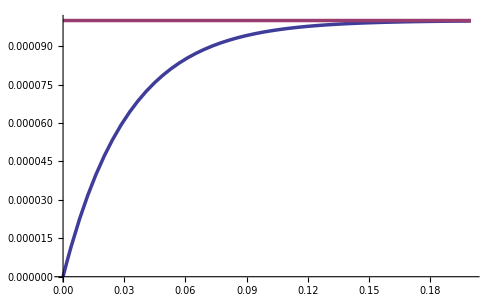

```mathematica
Plot[{c[x],ceq},{x,0,0.2},PlotRange->All,PlotStyle->Thickness[0.005]]
```

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
phi[x_,t_]:=If[t>tau,phi0 (1-Exp[-q (x-vf t)]),0];
```

```mathematica
phi[0.1,  t0]
```

-2.14861916729396×10^308

```mathematica
t0
```

3.1536×10^10

```mathematica
tau
```

4.40806×10^7

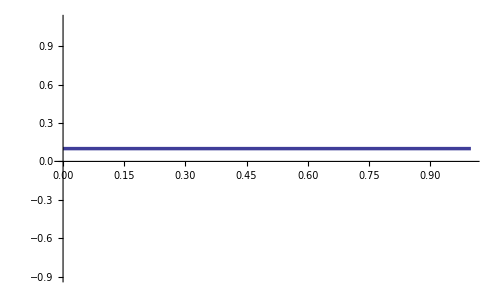

```mathematica
Plot[phi[x,2 t0],{x,0,1},PlotRange->All,PlotStyle->Thickness[0.005]]
```

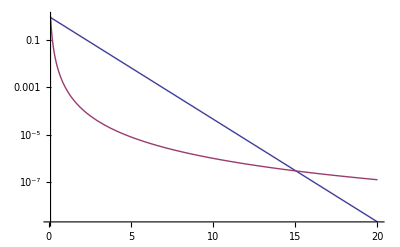

```mathematica
a=0.1;b=20;LogPlot[{Exp[-t],a^3t^-3},{t,a,b},PlotRange->All]
```

```mathematica
11421/2037.
```

5.60677

```mathematica
normal stop-run completed in 2037 steps
total iterations:4228,total cuts:0
cpu time=7.790 sec,0.1298 min,2.1639E-03 hours
```

```mathematica
115.49/7.79
```

14.8254

```mathematica
48981/4428.
```

11.0617